# Statistical Report

The data received included a total of 930,508 entries for invoices, 4,166 entries for items, and 50,000 revies in .dat files.

The invoice file contained information on Invoice id, date of invoice, item id (associated to the item sold), the id of the vendor, the name of the vendor, the id of the store, and store name, the address of the store, the city it was located, the zip code, the id of the county and its name, the number of bottles sold from the associated item.

The item file contained the item id, a description of it which presumably is the name, the category it fit into the number of bottles in a pack, the volume of the bottle, icost per bottle and the retail price.

```mathematica
RandomChoice[withPurchaseCost]
```

A few observations on counting the numbers of elements in each column in the invoice file

There seems to be a total of 1021 days when the purchases were done.

Apparently one item was not sold at all, the Yummy Surstromming Juice (item id 103)

There are 155 vendors

There is a discrepancy in the number of store ids (102) and store names (98). This last one being the same as addresses (98)

The invoices come from two main cities, (Davenport and Sioux City)

Spread across 14 zip codes

and two counties, (Scott and Wood bury)

The main interesting column by itself in terms of numeric analysis is the one corresponding to bottles sold.

On  approximately 9.87 bottles were sold per purchase

The standard deviation for the number of bottles sold was approximately 22.49

There were 73 sales marked as having sold 0 bottles, which seems to be an error

There is one sale of 2160 bottles of Yona’s Black Cherry soda in July 9 of 2012. That also seems like too much

In terms of dates, the following represents a Date list plot (timeseries plot) of the bottles sold each day

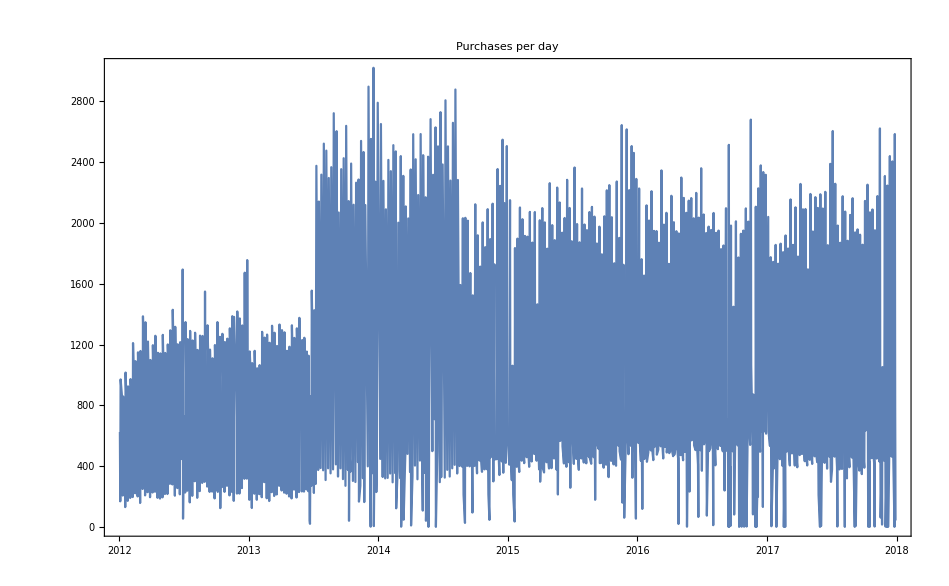

The above shows an interesting increase mid 2013 and a subsequent decrease mid 2014

We can further use a moving average on the data to remove some noise and see larger sclae trends

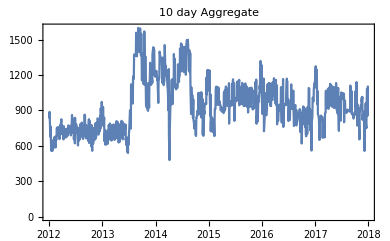

The graph suggests an increase in number of sales by end and beginning of each calendar year, aside from supporting the previous observation.